# Random Matrices and Quantum Chaos

Tomasz Andrzejewski

Random matrix theory (RMT) has been finding applications in number theory, finance, nuclear physics and quantum chaos. Here we give a short introduction to the concepts of random matrices and Gaussian ensembles and how they may be used to study chaotic behaviour of quantum systems, i.e. quantum chaos.

Quantum chaos tries to understand the nature of the wave-like motions for the electrons in atoms and molecules.  It leads to new insights in black hole information problem, thermalization and quantum simulation. A very important is a concept of an out-of-time-order correlator (OTOC).

## Random Matrix

A random matrix is a matrix whose elements are random numbers. 
Here we have a 4 by 4 matrix whose entries are independently sampled from Gaussian distribution (with mean 0 and variance 1):

```mathematica
M = RandomVariate[NormalDistribution[],{4,4}]; 
M // MatrixForm
```

(0.99322 | -1.97564 | -1.21885 | -0.824446
-1.09403 | 1.23839 | -1.38744 | -1.987
1.0245 | -0.351873 | -0.248714 | -0.924029
-0.463411 | 0.959629 | -0.949703 | -0.0376722)

However, there is no symmetry at this stage

```mathematica
Transpose[M] == M
```

False

Random matrix we usually study have some kind of underlying symmetry:

```mathematica
MSym = (M + Transpose[M]) / 2.
```

{{0.99322,-1.53483,-0.0971783,-0.643929},{-1.53483,1.23839,-0.869657,-0.513686},{-0.0971783,-0.869657,-0.248714,-0.936866},{-0.643929,-0.513686,-0.936866,-0.0376722}}

```mathematica
SymmetricMatrixQ[MSym]
```

True

And so we obtained our first random matrix drawn from the so-called Gaussian orthogonal ensemble (GOE).

## Density of eigenvalues

Now we construct and n x n (e.g. n = 3000) random real symmetric matrix, i.e. a random matrix sampled from a GOE distribution.

```mathematica
RandomVariate[GaussianOrthogonalMatrixDistribution[3000]];
```

We find its eigenvalues and plot their density.

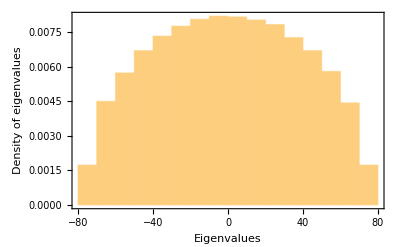

```mathematica
GOEDensity=Histogram[Eigenvalues[%],Automatic,"PDF",Frame->True,FrameLabel->{"Eigenvalues","Density of eigenvalues"},RotateLabel->False]
```

The density is clearly much lower near the edges of the range of values. For high-dimensional matrices the density of eigenvalues converges to the Wigner' s semicircle:

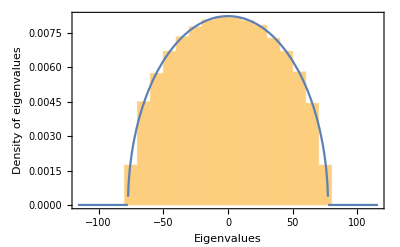

```mathematica
pValue=p/.FindDistributionParameters[sortedEvals,WignerSemicircleDistribution[p]];
WignerSemiCirclePlot=Plot[PDF[WignerSemicircleDistribution[pValue],x],{x,-1.5 pValue,1.5 pValue},PlotLegends->None];
Show[GOEDensity,WignerSemiCirclePlot,PlotRange->All ]
```

## Gaussian Ensembles

The Gaussian ensembles are families of normally distributed random matrices with distributions invariant under different unitary transformations.

Matrices from the Gaussian orthogonal ensemble (GOE) are symmetric.

```mathematica
goe=RandomVariate[GaussianOrthogonalMatrixDistribution[5]];
SymmetricMatrixQ[goe]
```

True

Matrices from the Gaussian unitary ensemble (GUE) are Hermitian.

```mathematica
gue=RandomVariate[GaussianUnitaryMatrixDistribution[5]];
HermitianMatrixQ[gue]
```

True

As we discussed earlier the density of eigenvalues of GOE in the limit of large dimension is a Wigner’s semicircle. We may compare the density of eigenvalues for GOE and GUE:

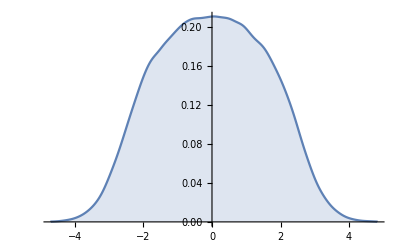
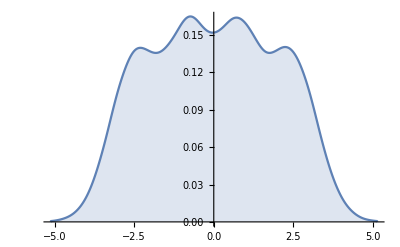

```mathematica
evalues=Flatten[RandomVariate[MatrixPropertyDistribution[Eigenvalues[x],x\[Distributed]#],10^5]]&/@{GaussianOrthogonalMatrixDistribution[4],GaussianUnitaryMatrixDistribution[4]};
Row[MapThread[SmoothHistogram[#1,Frame->None,PlotLegends->Placed[#2,Above],Filling->Axis,FillingStyle->Automatic]&,{evalues,{Style["Orthogonal",15],Style["Unitary",15]}}]]
```

The  spacings of eigenvalues (differences of consecutive eigenvalues) of matrix distributions follow a universal limiting form, so called Wigner surmise. It is observed in many systems for example in the energy-level spacings of heavy atoms. Below we compute the eigenvalue spacings of GUE:

```mathematica
dist = MatrixPropertyDistribution[Abs[Subtract @@ Eigenvalues[x]], x \[Distributed] GaussianUnitaryMatrixDistribution[2]];
spacings = Normalize[RandomVariate[dist,10000],Mean];
```

And we compare sample histogram with Wigner surmise (β = 2)

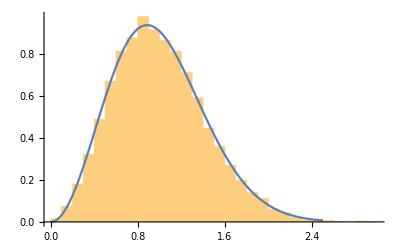

```mathematica
WignerSurmisePDF[x_, β : 2] := 2 (4x/Pi)^2 Exp[(-4/Pi)x^2]
Show[Histogram[spacings, {0.1}, PDF], Plot[WignerSurmisePDF[x,2],{x,0,2.5}]]
```

In the following we will focus on random Hermitian matrices, sampled from GUE, as Hermitian matrices represent physical observables in quantum mechanics.

## Exact Diagonalization

Exact diagonalization aims to solve the Schrödinger equation  of a quantum many body system numerically by finding a unitary transformation that makes the Hamiltonian diagonal. It is a powerful method in studying fermionic models, quantum magnets etc.

```mathematica
ExactDiagonalize[H_] := (Hvecs = Transpose[Normalize /@ Eigenvectors[Normal@H]]; invHvecs = Inverse[Hvecs]; diagH = Inverse[Hvecs].H.Hvecs;)
diagOp[op_] := Inverse[Hvecs].op.Hvecs;
```

## Out-of-time-order correlator (OTOC)

In recent years, the OTOC has been regarded as an important observable in the context of quantum gravity, quantum information scrambling and black holes. Similarly to Wigner distribution, the OTOC can be used as a measure of quantum chaos.  Its characteristics is that it saturates at the Ehrenfest time, which is defined by the time scale beyond which the wave function spreads over the whole system. Roughly speaking, Ehrenfest time is a boundary between a particle-like behavior and a wave-like behavior of the wave function.

OTOC is defined as thermal average of a commutator of Hermitian operators W and V: C(t) = -  <[W(t), V(0)]^2> where W(t) and V(t) are operators at time t in Heisenberg representation. Given a physical system defined by a Hamiltonian H and an initial state ,  we choose two Hermitian operators W and V and compare two states of the system that differ only in the timeordering of the operations used to create them.

```mathematica
OTOC[Wop_,Vop_,t_]:=1/N[dim] Tr[Hvecs.MatrixExp[-I t diagH].diagOp[Wop].MatrixExp[I t diagH].invHvecs.Vop.Hvecs.MatrixExp[-I t diagH].diagOp[Wop].MatrixExp[I t diagH].invHvecs.Vop]
```

```mathematica
OTOCPlot[Wop_,Vop_,st_,{tint_,tmax_,tstep_}]:=ListLinePlot[Table[{t,OTOC[Wop,Vop,t]},{t,tint,tmax,tstep}],PlotRange->Full,PlotLabel->StringJoin[st," OTOC"]];
```

Let us clear the Hamiltonian eigensystem:

```mathematica
ClearAll[H,Hvecs,invHvecs,diagH];
```

We now consider an ensemble of GUE Hamiltonians with 6 sites

```mathematica
sites=6;dim=2^sites;
```

We need to use SetDelayed so we get a new random matrix every time we evaluate:

```mathematica
H:=RandomVariate[GaussianUnitaryMatrixDistribution[dim]];
```

Exact diagonalize the Hamiltonian

```mathematica
ExactDiagonalize[H];
```

to plot the out-of-time-order correlator between the operators Z_1 and Z_6 defined as follows:

```mathematica
𝕀[n_]:=IdentityMatrix[2^n,SparseArray];
CircleTimes=KroneckerProduct;
Do[σ[a]=SparseArray@PauliMatrix[a],{a,0,3}]
X[n_]:=SparseArray[𝕀[n-1]⊗σ[1]⊗𝕀[sites-n]];
Y[n_]:=SparseArray[𝕀[n-1]⊗σ[2]⊗𝕀[sites-n]];
Z[n_]:=SparseArray[𝕀[n-1]⊗σ[3]⊗𝕀[sites-n]];
```

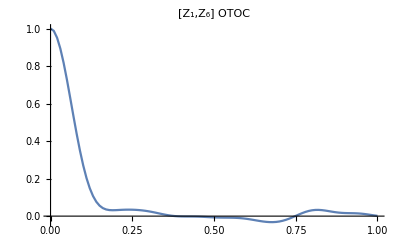

```mathematica
OTOCPlot[Z[1],Z[6],"[Z_1,Z_6]",{0,1,0.01}]
```

We may  compare it with a chaotic spin chain with open boundary conditions with n=6 sites. We shall use SparseArray to set up our Hamiltonian

```mathematica
h=0.5; g=-1.05;
```

The Hamiltonian of our system is given by a sum of the spin operators defined above in terms of Pauli matrices.

```mathematica
H =-(Sum[𝕀[n]⊗σ[3]⊗σ[3]⊗𝕀[sites-2-n],{n,0,sites-2}])- g Sum[𝕀[n]⊗σ[1]⊗𝕀[sites-1-n],{n,0,sites-1}]-h Sum[𝕀[n]⊗σ[3]⊗𝕀[sites-1-n],{n,0,sites-1}];
```

We now exact diagonalize the Hamiltonian

```mathematica
ExactDiagonalize[H]
```

to plot the out-of-time-order correlator between the operators Z_1 and Z_6

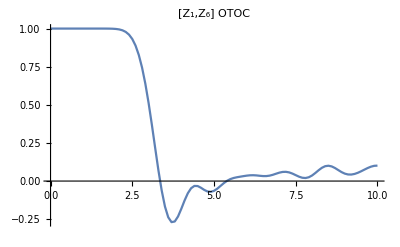

```mathematica
times={0,10,0.1};top={1,8,0.01};
OTOCPlot[Z[1],Z[6],"[Z_1,Z_6]",times]
```

We can observe the saturation at t~6s corresponding to the Ehrenfest time.

Random matrices may be further used in the study of quantum chaos to address questions in AdS/CFT correspondence, being particulary useful in SYK model.